# Polarization modulations

## 1. the function

```mathematica
alpha[ϵ_,δ_,χ_,η_,θ0_,B_,P_,t_]:=Module[{α},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
M=1.4*Ms;
R=10*km;
ω0=2π/P;
μ=(B R^3)/2;
I0=2/5*M*R^2;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
I1=I0;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
T=(4 I3 Sqrt[1+δ]EllipticK[m])/(ϵ L *Cos[θ0]);
cosθ=Cos[θ0]*JacobiDN[ωp*t,m];
sinθ=Sin[θ0]*(1+δ JacobiSN[ωp*t,m]^2)^0.5;
cosψ=(Sqrt[1+δ]JacobiSN[ωp*t,m])/Sqrt[1+δ JacobiSN[ωp*t,m]^2];
sinψ=JacobiCN[ωp*t,m]/Sqrt[1+δ JacobiSN[ωp*t,m]^2];
cosα=μ1*sinθ*sinψ+μ2*sinθ*cosψ+μ3*cosθ;
α=ArcCos[cosα];
α]
Radiative[ϵ_,ϵ1_,P_,B_,k_,M_,R_,χ_,η_,θ_]:=Module[{sol},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
ω0=2π/P;m=(B R^3)/2;τp=1/ω0/ϵ;I0=2/5*M*R^2;
sol=NDSolve[{u1'[t]==(ϵ1-ϵ)*ω0*u2[t]*u3[t]+1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u2[t]-Sin[η] Sin[χ] u3[t]),u2'[t]==(ϵ*ω0*u1[t]*u3[t]-1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u1[t]-Cos[η] Sin[χ] u3[t]))/(1+ϵ1), u3'[t]==(-ϵ1*ω0*u1[t]*u2[t]+1/(I0 *c^2 R)k m^2 ω0 Sin[χ] (Sin[η] u1[t]-Cos[η] u2[t]) (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]))/(1+ϵ),u1[0]==Sin[θ],u2[0]==0,u3[0]==Cos[θ]},{u1,u2,u3},{t,0,300*τp},Method->"ExplicitRungeKutta"]
; sol]

ϵ=1*10^-7;
δ=1;
ϵ1=((1+δ) (1+ϵ))/(1+δ+ϵ)-1;
P=2;
B=5*10^14;
k=0.6;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=45.0/180*π;
θ0=15/180.0*π;
τp=1/ω0/ϵ;
linearspace[a_,b_,n_]:=Range[a,b,(b-a)/n];
time=linearspace[0,10^8,2000];
s1=Flatten[alpha[ϵ,δ,χ,η,θ0,B,P,time]];

sol=Evaluate[Radiative[ϵ,ϵ1,P,B,k,M,R,χ,η,θ0]];
(*Plot[Evaluate[{u1[t],u2[t],u3[t]}/.sol],{t,0,100*τp},PlotTheme->
"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White,PlotLegends->{"u1","u2","u3"}]*)
ux=Flatten[{u1,u2,u3}/.sol][[1]];
uy=Flatten[{u1,u2,u3}/.sol][[2]];
uz=Flatten[{u1,u2,u3}/.sol][[3]];

L1=ux[time];
L2=uy[time];
L3=uz[time];
cosθ=L3;
sinθ=Sin[ArcCos[cosθ]];
cosψ=L2/(L1^2+L2^2)^0.5;
sinψ=L1/(L1^2+L2^2)^0.5;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
cosα=μ1*sinθ*sinψ+μ2*sinθ*cosψ+μ3*cosθ;
α=ArcCos[cosα];
data1=Transpose@{Flatten[time],s1,α};
SetDirectory[NotebookDirectory[]];
Export["triaxial_alpha1.dat",data1];
```

```mathematica
Remove["Global`*"]
ϵ=5*10^-7;
δ=1;
ϵ1=((1+δ) (1+ϵ))/(1+δ+ϵ)-1;
P=2;
B=2*10^14;
k=0.6;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=45.0/180*π;
θ0=15/180.0*π;
τp=1/ω0/ϵ;
linearspace[a_,b_,n_]:=Range[a,b,(b-a)/n];
Radiative[ϵ_,ϵ1_,P_,B_,k_,M_,R_,χ_,η_,θ_]:=Module[{sol},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
ω0=2π/P;m=(B R^3)/2;τp=1/ω0/ϵ;I0=2/5*M*R^2;
sol=NDSolve[{u1'[t]==(ϵ1-ϵ)*ω0*u2[t]*u3[t]+1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u2[t]-Sin[η] Sin[χ] u3[t]),u2'[t]==(ϵ*ω0*u1[t]*u3[t]-1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u1[t]-Cos[η] Sin[χ] u3[t]))/(1+ϵ1), u3'[t]==(-ϵ1*ω0*u1[t]*u2[t]+1/(I0 *c^2 R)k m^2 ω0 Sin[χ] (Sin[η] u1[t]-Cos[η] u2[t]) (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]))/(1+ϵ),u1[0]==Sin[θ],u2[0]==0,u3[0]==Cos[θ]},{u1,u2,u3},{t,0,300*τp},Method->"ExplicitRungeKutta"]
; sol]
sol=Evaluate[Radiative[ϵ,ϵ1,P,B,k,M,R,χ,η,θ0]];
(*Plot[Evaluate[{u1[t],u2[t],u3[t]}/.sol],{t,0,100*τp},PlotTheme->
"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White,PlotLegends->{"u1","u2","u3"}]*)
ux=Flatten[{u1,u2,u3}/.sol][[1]];
uy=Flatten[{u1,u2,u3}/.sol][[2]];
uz=Flatten[{u1,u2,u3}/.sol][[3]];
time=linearspace[0,10^8,2000];
L1=ux[time];
L2=uy[time];
L3=uz[time];
cosθ=L3;
sinθ=Sin[ArcCos[cosθ]];
cosψ=L2/(L1^2+L2^2)^0.5;
sinψ=L1/(L1^2+L2^2)^0.5;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
cosα=μ1*sinθ*sinψ+μ2*sinθ*cosψ+μ3*cosθ;
α=ArcCos[cosα];
```

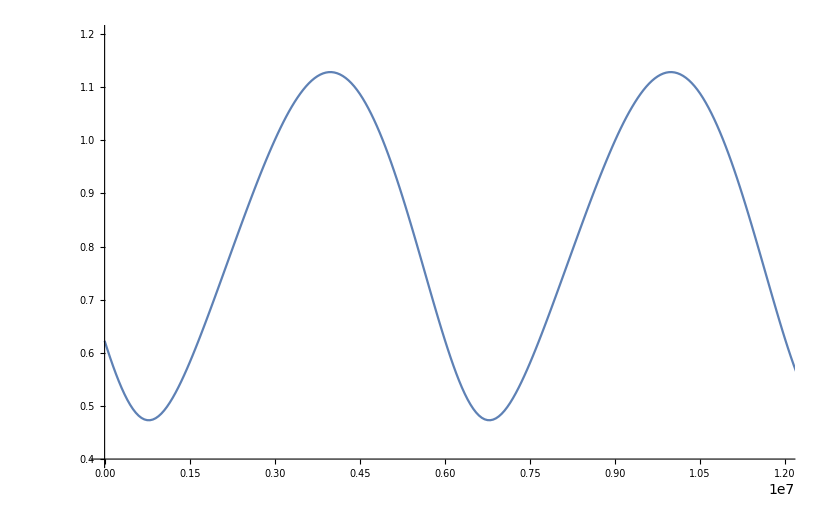

```mathematica
yr=31557600.0;
pd[ϵ_,δ_,χ_,η_,θ0_,P_]:=Module[{T},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
M=1.4*Ms;
R=10*km;
ω0=2π/P;
μ=(B R^3)/2;
I0=2/5*M*R^2;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
I1=I0;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
T=(4 I3 Sqrt[1+δ]EllipticK[m])/(ϵ L *Cos[θ0]);
T
]
T1=pd[ϵ,δ,χ,η,θ0,P];
αt=Transpose@{time,α};
ListPlot[αt,Joined->True,PlotRange->{{0,2*T1},{0.4,1.2}}]
```

```mathematica
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0(1+ϵ1),I0(1+ϵ)}];
m={Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ0],0,ω00*Cos[θ0]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Ltol=(Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2)^0.5;
Leff1=Ieff1*ωeff1/Ltol;
Leff2=Ieff2*ωeff2/Ltol;
Leff3=Ieff3*ωeff3/Ltol;
(*a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;*)
δeff=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
(*k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;*)
(*ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;*)
θ0eff=ArcSin[(Leff1^2+Leff2^2/(1+δeff))^0.5];
(*q is the modulus in the paper:m*)
q=δeff*Tan[θ0eff]^2;
ϕ0=-InverseJacobiCN[Leff1/Sin[θ0eff],q];
ϵeff=(Ieff3-Ieff1)/Ieff1;
T1=4*Ieff3/(ϵeff *Ltol*Cos[θ0eff])(1+δeff)^0.5 EllipticK[q]
```

6.00396×10^6

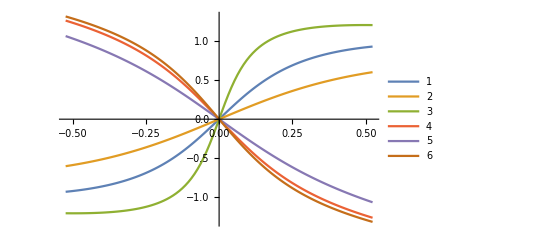

```mathematica
list=Transpose@{time,α};
f=Interpolation[list];
ι=45/180*π;
Φ=N[linearspace[-30/180*π,30/180*π,100]];

α1=f[0];
y1=Sin[α1]*Sin[Φ];
x1=Sin[ι]Cos[α1]-Cos[ι]Sin[α1]Cos[Φ];
Ψ1=ArcTan[y1/x1];
	
α2=f[T1/6];
y2=Sin[α2]*Sin[Φ];
x2=Sin[ι]Cos[α2]-Cos[ι]Sin[α2]Cos[Φ];
Ψ2=ArcTan[y2/x2];

α3=f[2T1/6];
y3=Sin[α3]*Sin[Φ];
x3=Sin[ι]Cos[α3]-Cos[ι]Sin[α3]Cos[Φ];
Ψ3=ArcTan[y3/x3];

α4=f[3T1/6];
y4=Sin[α4]*Sin[Φ];
x4=Sin[ι]Cos[α4]-Cos[ι]Sin[α4]Cos[Φ];
Ψ4=ArcTan[y4/x4];

α5=f[4T1/6];
y5=Sin[α5]*Sin[Φ];
x5=Sin[ι]Cos[α5]-Cos[ι]Sin[α5]Cos[Φ];
Ψ5=ArcTan[y5/x5];

α6=f[5T1/6];
y6=Sin[α6]*Sin[Φ];
x6=Sin[ι]Cos[α6]-Cos[ι]Sin[α6]Cos[Φ];
Ψ6=ArcTan[y6/x6];

list1=Transpose@{Φ,Ψ1};
list2=Transpose@{Φ,Ψ2};
list3=Transpose@{Φ,Ψ3};
list4=Transpose@{Φ,Ψ4};
list5=Transpose@{Φ,Ψ5};
list6=Transpose@{Φ,Ψ6};
ListPlot[{list1,list2,list3,list4,list5,list6},Joined->True,PlotLegends->Automatic]
rvm1=Transpose@{Φ,Ψ1,Ψ2,Ψ3,Ψ4,Ψ5,Ψ6};
SetDirectory[NotebookDirectory[]];
Export["rvm1.dat",rvm1];
```

```mathematica
time1=linearspace[0,3*T1,2000];
ι=Table[45/180*π,2001];
αx=f[time1];
βx=ι-αx;
rvm2=Transpose@{time1,αx,βx};
Export["rvm2.dat",rvm2];
```

```mathematica
yr=31557600.0;
T1/yr
```

0.190254